```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
voigt[x_,x0_,σ_,δ_,base_,A_]=base-A*PDF[VoigtDistribution[σ,δ],(x-x0)];
```

```mathematica
rawdata=Import["../data/steel/full_measure.csv","Table"];
```

```mathematica
fitdata=Table[{rawdata[[i]][[1]],1000*rawdata[[i]][[3]]/rawdata[[i]][[2]]},{i,1,Length[rawdata]}];
errordata=Table[1000*Sqrt[rawdata[[i]][[3]]]/rawdata[[i]][[2]],{i,1,Length[rawdata]}];
fitanderror=Table[{{rawdata[[i]][[1]],1000*rawdata[[i]][[3]]/rawdata[[i]][[2]]},ErrorBar[1000*Sqrt[rawdata[[i]][[3]]]/rawdata[[i]][[2]]]},{i,1,Length[rawdata]}];
```

```mathematica
fit=NonlinearModelFit[fitdata,voigt[x,x0,σ,δ,base,A],{{x0,0.1},{σ,0.02},{δ,0.1},{base,47.5},{A,0.5}},x,Weights->1/errordata^2]
```

Divide::infy: Infinite expression 2/(0.+0. ⅈ) encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ((0.+0. ⅈ) ComplexInfinity)/(√2) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NonlinearModelFit::nrjnum: The Jacobian is not a matrix of real numbers at {x0,σ,δ,base,A} = {0.179463,0.252535,0.0655315,47.4597,5.81316}.

FittedModel[47.4597-17.6946 (ⅇ^(116.431 («1»)^2) Erfc[10.7903 («19»-ⅈ («1»))]+«1» «1»)]

```mathematica
voigtfitplot=Plot[fit["BestFit"],{x,-2.5,2.5}];
dataplot=ListPlot[fitdata];
```

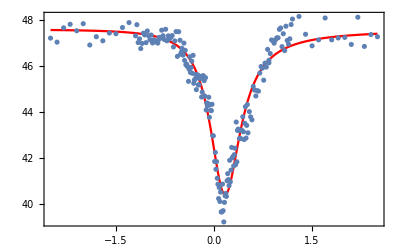

```mathematica
Show[{fitplot,dataplot},ImageSize->Full,PlotRange->All,Frame->True]
```

```mathematica
fit["BestFitParameters"]
fit["ParameterTable"]
```

{x0→0.179463,σ→0.252535,δ→0.0655315,base→47.4597,A→5.81316}

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 0.179463 | 0.00501016 | 35.8199 | 1.04715×10^-87
σ | 0.252535 | 0.0335294 | 7.53175 | 1.82109×10^-12
δ | 0.0655315 | 0.0491987 | 1.33198 | 0.184422
base | 47.4597 | 0.108197 | 438.643 | 6.03076×10^-294
A | 5.81316 | 0.39683 | 14.649 | 2.94278×10^-33

```mathematica
L[x_,x0_,A_,gamma_]=(2A/(Pi*gamma))/(1+4((x-x0)/gamma)^2);
```

```mathematica
G[x_,x0_,A_,gamma_]=A/gamma*Sqrt[4*Log[2]/Pi]*Exp[-4*Log[2]*((x-x0)/gamma)^2];
```

```mathematica
gammafunc[x_,x0_,e_,gamma0_]=2*gamma0/(1+Exp[e*(x-x0)]);
```

```mathematica
fitfunc[x_,x0_,base_,A_,e_,gamma0_,f_]=base-(f*L[x,x0,A,gammafunc[x,x0,e,gamma0]+(1-f)*G[x,x0,A,gammafunc[x,x0,e,gamma0]]]);
```

```mathematica
testfit=NonlinearModelFit[fitdata,{fitfunc[x,x0,base,A,a,gamma0,f],0<f<=1},{{x0,0.1},{base,47.5},{A,3},{a,-2},{gamma0,0.02},{f,0.8}},x,Weights->1/errordata^2];
testfit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 0.185689 | 0.00545095 | 34.0654 | 8.44086×10^-84
base | 47.5744 | 0.0970897 | 490.005 | 5.51406×10^-302
A | 6.43184 | 0.225517 | 28.5204 | 2.56527×10^-71
a | -0.772556 | 0.222188 | -3.47704 | 0.000625668
gamma0 | 0.573099 | 0.0709631 | 8.07602 | 6.93985×10^-14
f | 1. | 0.00679258 | 147.22 | 5.19337×10^-201

```mathematica
fitplot=Plot[testfit["BestFit"],{x,-2.5,2.5},PlotStyle->Red];
dataplot=ErrorListPlot[fitanderror,PlotStyle->{PointSize[0]}];
```

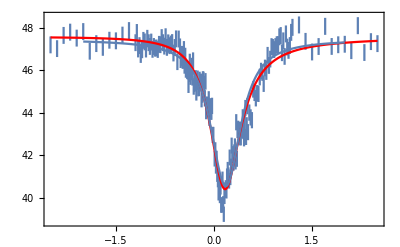

```mathematica
Show[{dataplot,fitplot,voigtfitplot},ImageSize->Full,PlotRange->All,Frame->True]
```